# Entanglement based QKD

```mathematica
ClearAll["Global`*"]
Import[NotebookDirectory[]<>"library_quantumInformation.m"];
```

## Defining state

#### Ideal state

```mathematica
idealState=1/√2(hh-vv);
rhoState=DensityMatrix[idealState];
DensityMatrixPlot[rhoState]
```

-Graphics3D-

```mathematica
ZZ={hh,hv,vh,vv};
ZX={hd,ha,va,vd};
ZY={hr,hl,vr,vl};
XZ={dh,dv,ah,av};
XX={dd,da,ad,aa};
XY={dr,dl,ar,al};
YZ={rh,rv,lh,lv};
YX={rd,ra,ld,la};
YY={rr,rl,lr,ll};
```

```mathematica
projectorsZ={"H","V"};
projectorsX={"D","A"};
projectorsY={"R","L"};
```

```mathematica
projectorsString={projectorsZ,projectorsX,projectorsY};
```

```mathematica
projectorsLabels=Flatten[Table[Flatten@Table[StringJoin[projectorsString⟦k⟧⟦i⟧,projectorsString⟦l⟧⟦j⟧],{i,1,2},{j,1,2}],{k,1,3},{l,1,3}],1]
```

{{HH,HV,VH,VV},{HD,HA,VD,VA},{HR,HL,VR,VL},{DH,DV,AH,AV},{DD,DA,AD,AA},{DR,DL,AR,AL},{RH,RV,LH,LV},{RD,RA,LD,LA},{RR,RL,LR,LL}}

```mathematica
measurementList={ZZ,ZX,ZY,XZ,XX,XY,YZ,YX,YY};
measurementListString={"ZZ","ZX","ZY","XZ","XX","XY","YZ","YX","YY"};
outcomes=Abs[Table[(#⟦i⟧†.idealState),{i,1,4}]&/@measurementList];
```

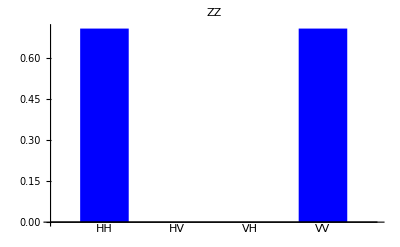
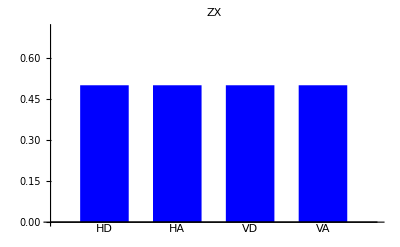
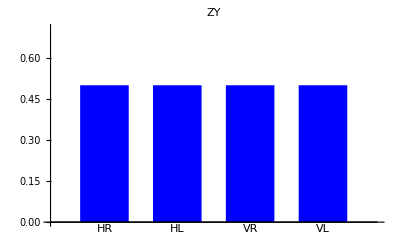
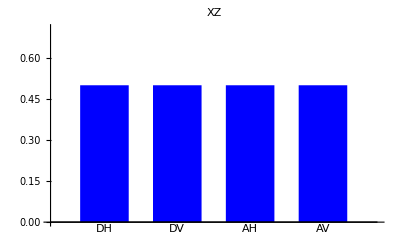
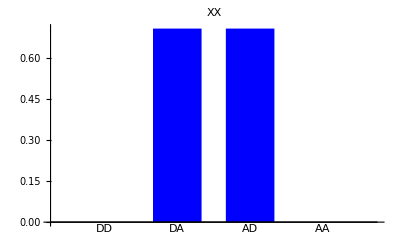
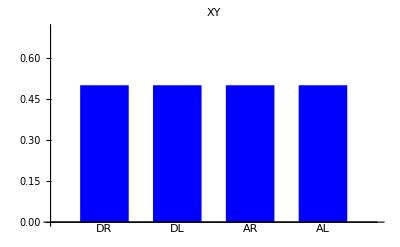
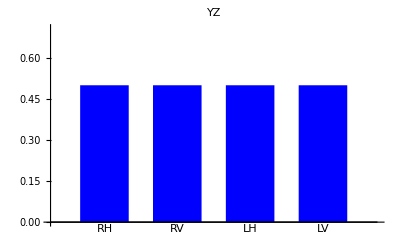
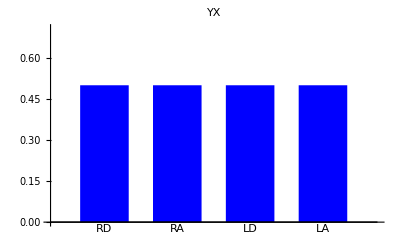

```mathematica
BarChart[Flatten[outcomes⟦#⟧],PlotRange->{0,1/√2},PlotLabel->measurementListString⟦#⟧,BarSpacing->Large,ChartBaseStyle->{EdgeForm[Opacity[0]],Blue},ChartLabels->projectorsLabels⟦#⟧]&/@Range@Length@outcomes
```

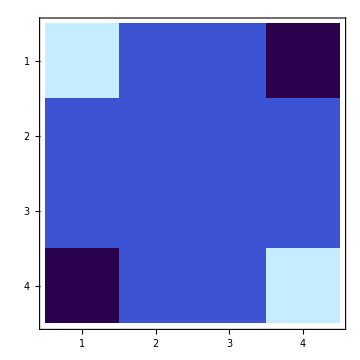

```mathematica
MatrixPlot[rhoState,ColorFunction->"DeepSeaColors"]
```

### Imbalanced quantum state in measured in two bases

```mathematica
ImbalancedState[x_]:=Block[{y},
	x*hh+NSolve[(x)^2+(y)^2==1,y]⟦2,1,2⟧*vv]
```

```mathematica
Manipulate[
DensityMatrixPlot[
DensityMatrix[ImbalancedState[a]]]
,{a,0,1}]
```

```mathematica
measurements={{hh,hv,vh,vv},{dd,da,ad,aa}};
measurementStrings={{"HH","HV","VH","VV"},{"DD","DA","AD","AA"}};
```

```mathematica
settingsPlot={
Frame->True
,ImageSize->200
,AspectRatio->1/0.5
,BarSpacing->Large
,PlotRange->{0,1}
,LabelStyle->Directive[FontFamily->"IBM Plex Mono",FontSize->16,Black]
,IntervalMarkers->"Fences"
,FrameLabel->{"",Style["outcome probability",FontFamily->"YuMincho"]}
,ChartStyle->Directive[Darker@Black,Opacity[1],EdgeForm[{Black,Thickness[0.001],Opacity[1]}]]
,ChartElementFunction->ChartElementDataFunction["SegmentScaleRectangle","Segments"->100,"ColorScheme"->"BlueGreenYellow"]};
```

```mathematica
bellStates={1/√2(hh+vv)
,1/√2(hh-vv)
,1/√2(hv+vh)
,1/√2(hv-vh)};
```

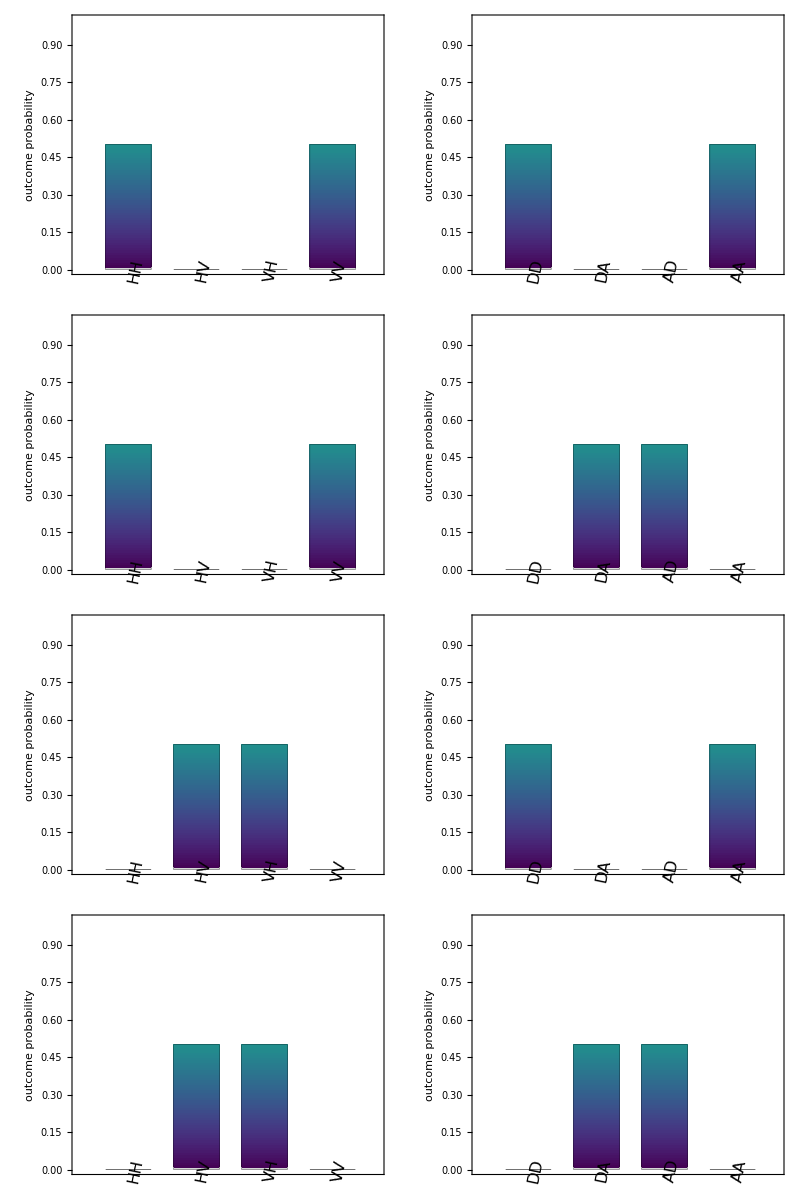

```mathematica
Table[{BarChart[ProjectionMeasurement[#,bellStates⟦i⟧]&/@measurements⟦1⟧,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦1⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
],
BarChart[ProjectionMeasurement[#,bellStates⟦i⟧]&/@measurements⟦2⟧,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦2⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]]},{i,1,4}]//TableForm
```

### Full plot QBER and Qx

```mathematica
Manipulate[
{BarChart[ProjectionMeasurement[#,ImbalancedState[a]]&/@measurements⟦1⟧,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦1⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}],
BarChart[ProjectionMeasurement[#,ImbalancedState[a]]&/@measurements⟦2⟧
,PlotRange->Automatic,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦2⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}],

("Qx = "<>ToString@(100*((1-ImbalancedState[a]†.Kron[sx,sx].ImbalancedState[a])/2)⟦1,1⟧)),
("QBER = "<>ToString@Chop@(100*((1-ImbalancedState[a]†.Kron[sz,sz].ImbalancedState[a])/2)⟦1,1⟧))

},
{a,0,1,0.00000001}]
```

#### Animation

```mathematica
iter=Join[Table[a,{a,0,1,0.01}],Table[a,{a,1,0,-0.01}]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.,0.99,0.98,0.97,0.96,0.95,0.94,0.93,0.92,0.91,0.9,0.89,0.88,0.87,0.86,0.85,0.84,0.83,0.82,0.81,0.8,0.79,0.78,0.77,0.76,0.75,0.74,0.73,0.72,0.71,0.7,0.69,0.68,0.67,0.66,0.65,0.64,0.63,0.62,0.61,0.6,0.59,0.58,0.57,0.56,0.55,0.54,0.53,0.52,0.51,0.5,0.49,0.48,0.47,0.46,0.45,0.44,0.43,0.42,0.41,0.4,0.39,0.38,0.37,0.36,0.35,0.34,0.33,0.32,0.31,0.3,0.29,0.28,0.27,0.26,0.25,0.24,0.23,0.22,0.21,0.2,0.19,0.18,0.17,0.16,0.15,0.14,0.13,0.12,0.11,0.1,0.09,0.08,0.07,0.06,0.05,0.04,0.03,0.02,0.01,0.}

```mathematica
testIter=1;
```

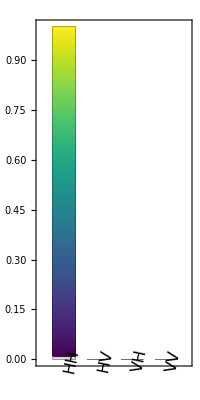
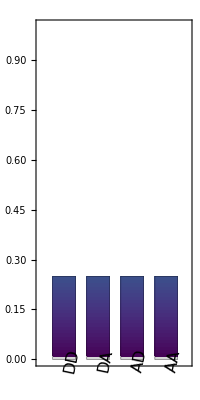
{{-Graphics-,-Graphics-,QBER_z = 0,QBER_x = 50.}}

```mathematica
animationExport=Table[

{BarChart[
ProjectionMeasurement[#,ImbalancedState[a]]&/@measurements⟦1⟧,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦1⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}
],

BarChart[
ProjectionMeasurement[#,ImbalancedState[a]]&/@measurements⟦2⟧
,(*PlotRange->Automatic,*)
settingsPlot,
ChartLabels->Placed[measurementStrings⟦2⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}
],

("QBER_z = "<>ToString@Chop@(100*((1-ImbalancedState[a]†.Kron[sz,sz].ImbalancedState[a])/2)⟦1,1⟧)),
("QBER_x = "<>ToString@(100*((1-ImbalancedState[a]†.Kron[sx,sx].ImbalancedState[a])/2)⟦1,1⟧))

},

{a,testIter}]
```

```mathematica
Export[NotebookDirectory[]<>"animation.gif",animationExport]
```

/Users/alexanderpickston/Documents/GitHub/QIPmma/State preparation/animation.gif

### Depolarizing noise

```mathematica
DepolControl[p_,ρ_]:=(1-3/4*p) ρ+p/4*(cX.ρ.cX+cY.ρ.cY+cZ.ρ.cZ);
```

```mathematica
Manipulate[DensityMatrixPlot[DepolControl[a,DensityMatrix@bellStates⟦1⟧]]
,{a,0,1}]
```

```mathematica
Manipulate[
{BarChart[ProjectionMeasurement[#,DepolControl[a,DensityMatrix@bellStates⟦1⟧]]&/@measurements⟦1⟧
,PlotRange->Automatic,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦1⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}]

,BarChart[ProjectionMeasurement[#,DepolControl[a,DensityMatrix@bellStates⟦1⟧]]&/@measurements⟦2⟧
,PlotRange->Automatic,
settingsPlot,
ChartLabels->Placed[measurementStrings⟦2⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&],
FrameLabel->{"",Style["p",FontFamily->"YuMincho"]}],

(*Born rule for operating on the density operator of the state*)

("Qx = "<>ToString@Chop@(100*((1-Tr[DepolControl[a,DensityMatrix@bellStates⟦1⟧].Kron[sx,sx]])/2))),
("QBER = "<>ToString@Chop@(100*((1-Tr[DepolControl[a,DensityMatrix@bellStates⟦1⟧].Kron[sz,sz]])/2)))

},
{a,0,1,0.00000001}]
```